# Mapeo de Hénon

Definido por el sistema de ecuaciones en diferencias


donde  y  son parámetros reales.
Fijamos  y , escogemos una condición inicial, y nos fijamos en donde caen los iterados sucesivos.

```mathematica
henon=RecurrenceTable[{x[n+1]==y[n]+1-1.4*x[n]^2,y[n+1]==0.3*x[n],x[1]==0,y[1]==-0.2},{x,y},{n,1,1000}];
```

```mathematica
figframes=ParallelTable[ListPlot[henon[[1;;m]],PlotRange->{{-1.5,1.5},{-0.4,0.4}},AxesLabel->{x[n],y[n]},PlotStyle->PointSize[Small]],{m,1,1000}];
```

```mathematica
ListAnimate[figframes]
```

Iteramos muchas veces y vemos la estructura del atractor:

```mathematica
henonbig=RecurrenceTable[{x[n+1]==y[n]+1-1.4*x[n]^2,y[n+1]==0.3*x[n],x[1]==0,y[1]==-0.2},{x,y},{n,1,1000000}];
```

```mathematica
Show[{ListPlot[henonbig,AxesLabel->{x[n],y[n]},Epilog->{Directive[Red],Line[{{0.53,0.15},{0.53,0.21}}],Line[{{0.74,0.15},{0.74,0.21}}]}],Plot[0.21,{x,0.53,0.74},PlotStyle->Red],Plot[0.15,{x,0.53,0.74},PlotStyle->Red]}]
```

-Graphics-

```mathematica
Show[{ListPlot[henonbig,AxesLabel->{x[n],y[n]},PlotRange->{{0.53,0.74},{0.15,0.21}},Epilog->{Directive[Red],Line[{{0.62,0.185},{0.62,0.191}}],Line[{{0.64,0.185},{0.64,0.191}}]}],Plot[0.191,{x,0.62,0.64},PlotStyle->Red],Plot[0.185,{x,0.62,0.64},PlotStyle->Red]}]
```

-Graphics-

```mathematica
ListPlot[henonbig,AxesLabel->{x[n],y[n]},PlotRange->{{0.62,0.64},{0.185,0.191}}]
```

-Graphics-

Ahora, calculamos las soluciones de equilibrio del sistema con los parámetros usados anteriormente:

```mathematica
Solve[{x==y+1-(14/10)*x^2,y==(3/10)*x},{x,y}]
```

{{x→1/28 (-7-√609),y→3/280 (-7-√609)},{x→1/28 (-7+√609),y→3/280 (-7+√609)}}

```mathematica
N[{{x->1/28 (-7-√609),y->3/280 (-7-√609)},{x->1/28 (-7+√609),y->3/280 (-7+√609)}}]
```

{{x→-1.13135,y→-0.339406},{x→0.631354,y→0.189406}}

Hay dos puntos de equilibrio, uno en el primer cuadrante y otro en el tercer cuadrante. Calculamos los eigenvalores y eigenvectores en ambos casos:

```mathematica
N[Eigensystem[{{-2*(14/10)*x,1},{3/10,0}}/.{x->1/28 (-7-√609),y->3/280 (-7-√609)}]]
```

{{3.25982,-0.0920296},{{10.8661,1.},{-0.306765,1.}}}

```mathematica
N[Eigensystem[{{-2*(14/10)*x,1},{3/10,0}}/.{x->1/28 (-7+√609),y->3/280 (-7+√609)}]]
```

{{-1.92374,0.155946},{{-6.41246,1.},{0.519821,1.}}}

En ambos casos tenemos un eigenvalor con  y otro con , sin embargo, uno de ellos es positivo y otro es negativo, por lo que ambos puntos de equilibro corresponden a un nuevo tipo, al que podríamos llamar ciclo-silla. Ahora visualizamos los puntos de equilibrio así como sus respectivos eigenvectores:

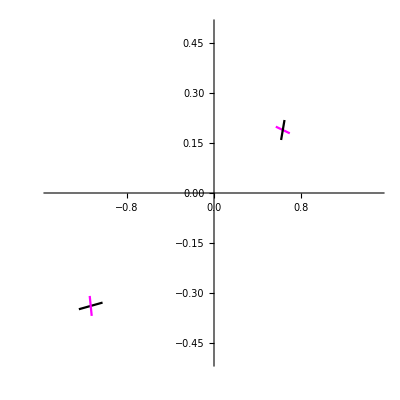

```mathematica
Show[{ParametricPlot[{1/28 (-7-√609)+1/6 (7+√609+√(2 (389+7 √609)))*t,3/280 (-7-√609)+t},{t,-0.01,0.01},PlotStyle->Black,PlotRange->{{-1.5,1.5},{-0.5,0.5}},AspectRatio->1],ParametricPlot[{1/28 (-7-√609)+1/6 (7+√609-√(2 (389+7 √609)))*t,3/280 (-7-√609)+t},{t,-0.03,0.03},PlotStyle->Magenta],ParametricPlot[{1/28 (-7+√609)+1/6 (7-√609-√(2 (389-7 √609)))*t,3/280 (-7+√609)+t},{t,-0.01,0.01},PlotStyle->Magenta],ParametricPlot[{1/28 (-7+√609)+1/6 (7-√609+√(2 (389-7 √609)))*t,3/280 (-7+√609)+t},{t,-0.03,0.03},PlotStyle->Black]}]
```

Ahora, observamos el comportamiento de las soluciones cerca de los puntos de equilibrio a lo largo de los eigenvectores repulsivos:

```mathematica
sol1=RecurrenceTable[{x[n+1]==y[n]+1-(14/10)*x[n]^2,y[n+1]==(3/10)*x[n],x[1]==1/28 (-7-√609)+10.866073659638175*0.0000000001,y[1]==3/280 (-7-√609)+0.0000000001},{x,y},{n,20}];
sol2=RecurrenceTable[{x[n+1]==y[n]+1-(14/10)*x[n]^2,y[n+1]==(3/10)*x[n],x[1]==1/28 (-7+√609)-6.412462860511356*0.0000000001,y[1]==3/280 (-7+√609)+0.0000000001},{x,y},{n,32}];
```

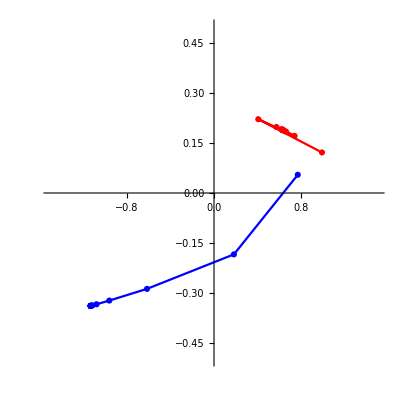

```mathematica
ListPlot[{sol1,sol2},PlotRange->{{-1.5,1.5},{-0.5,0.5}},AspectRatio->1,PlotStyle->{Blue,Red},Joined->True,Mesh->All]
```

Y ahora las vemos sobre el atractor:

```mathematica
Show[{ListPlot[henonbig,AxesLabel->{x[n],y[n]}],ListPlot[{sol1,sol2},PlotRange->{{-1.5,1.5},{-0.5,0.5}},AspectRatio->1,PlotStyle->{Blue,Red},Joined->True,Mesh->All]}]
```

-Graphics-